We call the package Olsson.wl

```mathematica
<<Olsson_new.wl
```

Olsson.wl v1.1
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

ROC2.wl v1.1
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

## Block 1 : Derivation of ACs around (∞,0) and (∞,∞)

### Derivation of the AC around (∞,0) :

The KdF is defined here.

```mathematica
Subscript[KdFAC, 1][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]);
```

We find the region of convergence (ROC) using callroc command

```mathematica
callroc[{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n])]//FullSimplify
```

{{{{m+n,m+n,m},{m,m,n}},{x,y}}}

{√Abs[x]+√Abs[y]<1}

Its region of convergence (ROC) is given by

```mathematica
Subscript[KdFROC, 1][x_,y_]=√Abs[x]+√Abs[y]<1;
```

Performing the summation over the variable m by using the option sum -> True

```mathematica
Olsson[1,{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]),sum-> True]
```

(y^n HypergeometricPFQ[{b1,a1+n,a2+n},{c1,c2},x] Pochhammer[a1,n] Pochhammer[a2,n])/(n! Pochhammer[d1,n])

We observe the presence of _3 F_2 .

To apply the analytic continuation of _3 F_2(x) at x=∞, we use the inf-> True option.
Further simplifying the Pochhammer symbols using the option sim-> True,
the ROC of convergence is obtained using the roc-> True  option

```mathematica
Olsson[1,{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]),inf-> True,sim-> True,roc-> True]//Simplify//Expand
```

{{{{m+n,m+n,m+n},{m,m+n,n}},{1/x,y/x}},{{{m,m,m},{m-n,m-n,n}},{1/x,y}}}

{1/Abs[x]<1&&1+√Abs[y]<√Abs[x]&&Abs[y]<1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1,((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b1] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b1] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b1,m+n] Pochhammer[d1,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b1] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b1] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b1,m+n] Pochhammer[d1,n])+((-x)^-b1 x^-m y^n Gamma[a1-b1] Gamma[a2-b1] Gamma[c1] Gamma[c2] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Pochhammer[1-a1+b1,m-n] Pochhammer[1-a2+b1,m-n] Pochhammer[d1,n])}

The output is a list containing two elements. The last element is the expression of the AC around (∞,0) and the first one is its ROC.

Lets store the obtained AC as

```mathematica
Subscript[KdFAC, 2][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b1] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b1] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b1,m+n] Pochhammer[d1,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b1] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b1] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b1,m+n] Pochhammer[d1,n])+((-x)^-b1 x^-m y^n Gamma[a1-b1] Gamma[a2-b1] Gamma[c1] Gamma[c2] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Pochhammer[1-a1+b1,m-n] Pochhammer[1-a2+b1,m-n] Pochhammer[d1,n]);
```

```mathematica
Subscript[KdFROC, 2][x_,y_]=1/Abs[x]<1&&1+√Abs[y]<√Abs[x]&&Abs[y]<1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1;
```

We plot the KdFROC_1 and KdFROC_2 below

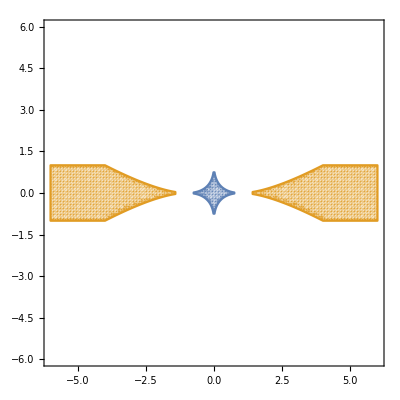

```mathematica
RegionPlot[{Subscript[KdFROC, 1][x,y],Subscript[KdFROC, 2][x,y]},{x,-6,6},{y,-6,6},PlotPoints->100]
```

### Derivation of the AC around (∞,∞) :

The AC of the KdF function around (∞, 0) is the sum of three series. Let us denote those as S1,S2 and S3

```mathematica
{S1,S2,S3}=List@@Expand[Subscript[KdFAC, 2][a1,a2,b,c1,c2,d,x,y,m,n]]
```

{((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b,m+n] Pochhammer[d,n]),((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b,m+n] Pochhammer[d,n]),((-x)^-b x^-m y^n Gamma[a1-b] Gamma[a2-b] Gamma[c1] Gamma[c2] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Pochhammer[1-a1+b,m-n] Pochhammer[1-a2+b,m-n] Pochhammer[d,n])}

We find the ROC of each of the series S1,S2 and S3

```mathematica
SROCs = Flatten[Simplify[callroc[{m,n},#]&/@{S1,S2,S3}]]
```

{{{{m+n,m+n,m+n},{m,m+n,n}},{1/x,y/x}}}

{{{{m+n,m+n,m+n},{m,m+n,n}},{1/x,y/x}}}

{{{{m,m,m},{m-n,m-n,n}},{1/x,y}}}

{Abs[x]>1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1,Abs[x]>1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1,1/Abs[x]<1&&1+√Abs[y]<√Abs[x]&&Abs[y]<1}

Let us plot the ROCs of S1, S2 and S3 for real values of x,y

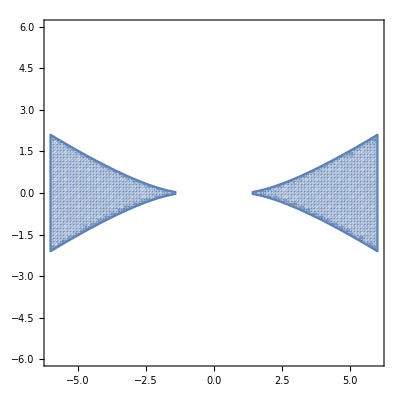
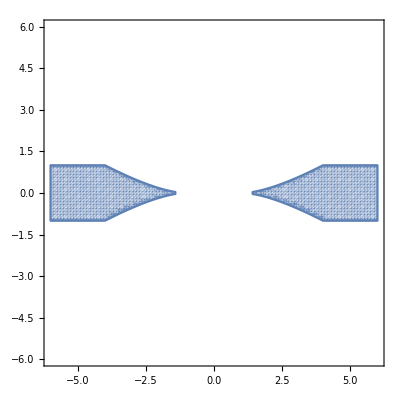
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
RegionPlot[#,{x,-6,6},{y,-6,6},PlotPoints->100]&/@SROCs
```

It is to be noticed that from the ROCs above that the series S3 can be analytically continued further.

We take S2 and take the summation of index n, using the sum-> True option

```mathematica
Olsson[2,{m,n},S3,sum-> True]
```

((-x)^-b x^-m Gamma[a1-b] Gamma[a2-b] Gamma[c1] Gamma[c2] HypergeometricPFQ[{a1-b-m,a2-b-m},{d},y] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m])/(m! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Pochhammer[1-a1+b,m] Pochhammer[1-a2+b,m])

Now using the AC of the Gauss _2 F_1(y) around y=∞, we find two series.

```mathematica
Olsson[2,{m,n},S3,inf-> True,sim-> True,roc-> True]
```

{{{{-m+n,m,m,m,-m+n},{n}},{y/x,1/y}}}

{Abs[y/x]<1&&1/(√Abs[y])<-1+1/(√Abs[y/x])&&1/Abs[y]<1,((-1)^m (-x)^-b x^-m (-y)^(-a1+b+m) y^-n Gamma[-a1+a2] Gamma[a1-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a1-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a1-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a1+b+d] Pochhammer[1+a1-a2,n])+((-1)^m (-x)^-b x^-m (-y)^(-a2+b+m) y^-n Gamma[a1-a2] Gamma[a2-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a2-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a2-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a2+b+d] Pochhammer[1-a1+a2,n])}

Let us store denote those by S31 and S32

```mathematica
{S31,S32}=List@@(((-1)^m (-x)^-b x^-m (-y)^(-a1+b+m) y^-n Gamma[-a1+a2] Gamma[a1-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a1-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a1-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a1+b+d] Pochhammer[1+a1-a2,n])+((-1)^m (-x)^-b x^-m (-y)^(-a2+b+m) y^-n Gamma[a1-a2] Gamma[a2-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a2-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a2-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a2+b+d] Pochhammer[1-a1+a2,n]));
```

Let us plot it ROC below

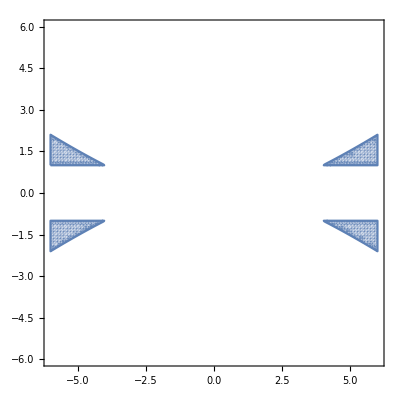

```mathematica
RegionPlot[Abs[y/x]<1&&1/(√Abs[y])<-1+1/(√Abs[y/x])&&1/Abs[y]<1,{x,-6,6},{y,-6,6},PlotPoints->100]
```

Hence the (∞,∞) AC of KdF is found to be the sum of S1, S2, S31 and S32

```mathematica
S1+S2+S31+S32
```

((-1)^m (-x)^-b x^-m (-y)^(-a1+b+m) y^-n Gamma[-a1+a2] Gamma[a1-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a1-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a1-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a1+b+d] Pochhammer[1+a1-a2,n])+((-1)^m (-x)^-b x^-m (-y)^(-a2+b+m) y^-n Gamma[a1-a2] Gamma[a2-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a2-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a2-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a2+b+d] Pochhammer[1-a1+a2,n])+((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b,m+n] Pochhammer[d,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b,m+n] Pochhammer[d,n])

We denote the AC of the KdF function around (∞,∞) as KdFAC_3 below

```mathematica
Subscript[KdFAC, 3][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^m (-x)^-b x^-m (-y)^(-a1+b+m) y^-n Gamma[-a1+a2] Gamma[a1-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a1-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a1-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a1+b+d] Pochhammer[1+a1-a2,n])+((-1)^m (-x)^-b x^-m (-y)^(-a2+b+m) y^-n Gamma[a1-a2] Gamma[a2-b] Gamma[c1] Gamma[c2] Gamma[d] Pochhammer[a2-b,-m+n] Pochhammer[b,m] Pochhammer[1+b-c1,m] Pochhammer[1+b-c2,m] Pochhammer[1+a2-b-d,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b+c1] Gamma[-b+c2] Gamma[-a2+b+d] Pochhammer[1-a1+a2,n])+((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b,m+n] Pochhammer[d,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b,m+n] Pochhammer[d,n]);
```

The ROC of the above AC is the intersection of the ROCs of S1, S2, S31 and S32 . Thus calling the callroc command we find the ROC of each of these series and then we take the intersection of those four ROCs to find the ROC of the AC of the KdF function around (∞,∞).

```mathematica
Simplify[And@@Flatten[callroc[{m,n},#]&/@{S1,S2,S31,S32}]]
```

{{{{m+n,m+n,m+n},{m,m+n,n}},{1/x,y/x}}}

{{{{m+n,m+n,m+n},{m,m+n,n}},{1/x,y/x}}}

{{{{-m+n,m,m,m,-m+n},{n}},{y/x,1/y}}}

{{{{-m+n,m,m,m,-m+n},{n}},{y/x,1/y}}}

1/Abs[x]<1&&1/Abs[y]<1&&1+1/(√Abs[y])<1/(√Abs[y/x])&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1

Let us denote it as KdFROC_3.

```mathematica
Subscript[KdFROC, 3][x_,y_]=1/Abs[x]<1&&1/Abs[y]<1&&1+1/(√Abs[y])<1/(√Abs[y/x])&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1;
```

## Block 2 : Derivation of the ACs around (0,1)

### Derivation of the first AC around (0,1) :

Starting from the definition of the KdF function, we find the AC of KdF around (0,1) by taking the summation over the index n and using the AC of _2 F_1(y) around y=1

```mathematica
Olsson[2,{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]),one-> True,sim-> True,roc-> True]
```

{{{{m+n,m+n,m,m,m},{m,m,2 m+n}},{x,1-y}},{{{m,m,m,-m+n,-m+n},{m,m,-2 m+n}},{x/(-1+y)^2,1-y}}}

{√Abs[1-y]<1&&((√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y]&&√Abs[x]<1)||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2))&&Abs[x/(-1+y)^2]<1/4&&√Abs[1-y]<(√(1-2 √Abs[x/(-1+y)^2]))/(√Abs[x/(-1+y)^2])&&Abs[1-y]<1,(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(x^m (1-y)^(-a1-a2+d1-2 m+n) Gamma[a1+a2-d1] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m] Pochhammer[-a1+d1,-m+n] Pochhammer[-a2+d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1-a1-a2+d1,-2 m+n])}

Let us denote this AC as KdFAC_4 and its corresponding ROC as KdFROC_4 below

```mathematica
Subscript[KdFAC, 4][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(x^m (1-y)^(-a1-a2+d1-2 m+n) Gamma[a1+a2-d1] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m] Pochhammer[-a1+d1,-m+n] Pochhammer[-a2+d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1-a1-a2+d1,-2 m+n]);
```

```mathematica
Subscript[KdFROC, 4][x_,y_]=√Abs[1-y]<1&&((√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y]&&√Abs[x]<1)||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2))&&Abs[x/(-1+y)^2]<1/4&&√Abs[1-y]<(√(1-2 √Abs[x/(-1+y)^2]))/(√Abs[x/(-1+y)^2])&&Abs[1-y]<1;
```

### Derivation of the second AC around (0,1) :

The first AC around the point (0,1) is a sum of two series. Let us denote those by T1 and T2

```mathematica
{T1,T2}=List@@((x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(x^m (1-y)^(-a1-a2+d1-2 m+n) Gamma[a1+a2-d1] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m] Pochhammer[-a1+d1,-m+n] Pochhammer[-a2+d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1-a1-a2+d1,-2 m+n]));
```

Next we find the ROC of each of the series T1 and T2 using the callroc command

```mathematica
TROCs=Flatten[callroc[{m,n},#]&/@{T1,T2}]
```

{{{{m+n,m+n,m,m,m},{m,m,2 m+n}},{x,1-y}}}

{{{{m,m,m,-m+n,-m+n},{m,m,-2 m+n}},{x/(-1+y)^2,1-y}}}

{√Abs[1-y]<1&&((√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y]&&√Abs[x]<1)||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2)),Abs[x/(-1+y)^2]<1/4&&√Abs[1-y]<(√(1-2 √Abs[x/(-1+y)^2]))/(√Abs[x/(-1+y)^2])&&Abs[1-y]<1}

Plotting the above two ROCs below

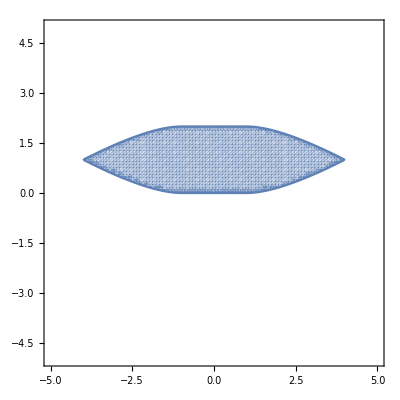
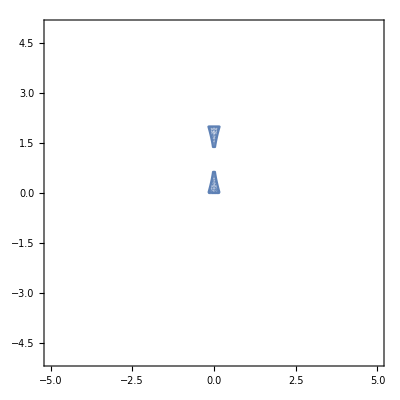

```mathematica
RegionPlot[#,{x,-5,5},{y,-5,5},PlotPoints->100]&/@TROCs
```

We observe that the series T2 can be analytically continued further. 
We take the summation over the variable m. Note the appearance of the _5 F_4.

```mathematica
Olsson[1,{m,n},T2,sum-> True]
```

((1-y)^(-a1-a2+d1+n) Gamma[a1+a2-d1] Gamma[d1] HypergeometricPFQ[{b1,1+a1-d1,1+a2-d1,a1/2+a2/2-d1/2-n/2,1/2+a1/2+a2/2-d1/2-n/2},{c1,c2,1+a1-d1-n,1+a2-d1-n},(4 x)/(1-y)^2] Pochhammer[-a1+d1,n] Pochhammer[-a2+d1,n])/(n! Gamma[a1] Gamma[a2] Pochhammer[1-a1-a2+d1,n])

Using the analytic continuation of the _5 F_4(z) with z=(4 x)/(1-y)^2 around z=∞, we find three non-vanishing series. Let us store those as T21, T22 and T23

```mathematica
{T21,T22,T23}=List@@(Olsson[1,{m,n},T2,inf-> True,sim-> True])
```

{(4^(-b1-m) (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^-b1 ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[1/2 (a1+a2-2 b1-d1)] Gamma[1/2 (1+a1+a2-2 b1-d1)] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1/2 (a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (1+a1+a2-2 b1-d1),-n/2] Pochhammer[-a1+b1+d1,m+n] Pochhammer[-a2+b1+d1,m+n] Pochhammer[1/2 (1-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (1+a1+a2-d1)] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[-a1+b1+d1,m] Pochhammer[-a2+b1+d1,m] Pochhammer[1/2 (1-a1-a2+2 b1+d1),m+n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),m+n/2]),(2^(-a1-a2-2 m) √π (2-2 y)^(d1+n) (1-y)^(-a1-a2) (-x/(-1+y)^2)^(1/2 (1-a1-a2+d1+n)) ((-1+y)^2/x)^(1+m) Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-1-a1-a2+2 b1+d1)] Pochhammer[1/2 (1+a1-a2-d1),n/2] Pochhammer[1/2 (1-a1+a2-d1),n/2] Pochhammer[1/2 (1+a1+a2-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),m+n/2] Pochhammer[1/2 (1+a1-a2+d1),-n/2] Pochhammer[1/2 (1-a1+a2+d1),m+n/2] Pochhammer[1/2 (1-a1+a2+d1),-n/2] Pochhammer[1/2 (-1-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (-1-a1-a2+2 c1+d1)] Gamma[1/2 (-1-a1-a2+2 c2+d1)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a1-a2-d1),-n/2] Pochhammer[1/2 (1-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (1+a1-a2+d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),n/2] Pochhammer[1/2 (1-a1+a2+d1),m-n/2] Pochhammer[1/2 (1-a1+a2+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c2+d1),n/2]),(2^(-a1-a2+d1-2 m+n) √π (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^(1/2 (-a1-a2+d1+n)) ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-a1-a2+2 b1+d1)] Pochhammer[1/2 (2+a1-a2-d1),n/2] Pochhammer[1/2 (2-a1+a2-d1),n/2] Pochhammer[1/2 (a1+a2-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),m+n/2] Pochhammer[1/2 (a1-a2+d1),-n/2] Pochhammer[1/2 (-a1+a2+d1),m+n/2] Pochhammer[1/2 (-a1+a2+d1),-n/2] Pochhammer[1/2 (-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (1+a1+a2-d1)] Gamma[1/2 (-a1-a2+2 c1+d1)] Gamma[1/2 (-a1-a2+2 c2+d1)] Pochhammer[1/2,m] Pochhammer[1/2 (2+a1-a2-d1),-n/2] Pochhammer[1/2 (2-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (a1-a2+d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),n/2] Pochhammer[1/2 (-a1+a2+d1),m-n/2] Pochhammer[1/2 (-a1+a2+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c2+d1),n/2])}

Thus the second AC of the KdF function around (0,1) is the sum of four series T1, T21, T22  and T23

```mathematica
T1+T21+T22+T23
```

(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(4^(-b1-m) (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^-b1 ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[1/2 (a1+a2-2 b1-d1)] Gamma[1/2 (1+a1+a2-2 b1-d1)] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1/2 (a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (1+a1+a2-2 b1-d1),-n/2] Pochhammer[-a1+b1+d1,m+n] Pochhammer[-a2+b1+d1,m+n] Pochhammer[1/2 (1-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (1+a1+a2-d1)] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[-a1+b1+d1,m] Pochhammer[-a2+b1+d1,m] Pochhammer[1/2 (1-a1-a2+2 b1+d1),m+n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),m+n/2])+(2^(-a1-a2-2 m) √π (2-2 y)^(d1+n) (1-y)^(-a1-a2) (-x/(-1+y)^2)^(1/2 (1-a1-a2+d1+n)) ((-1+y)^2/x)^(1+m) Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-1-a1-a2+2 b1+d1)] Pochhammer[1/2 (1+a1-a2-d1),n/2] Pochhammer[1/2 (1-a1+a2-d1),n/2] Pochhammer[1/2 (1+a1+a2-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),m+n/2] Pochhammer[1/2 (1+a1-a2+d1),-n/2] Pochhammer[1/2 (1-a1+a2+d1),m+n/2] Pochhammer[1/2 (1-a1+a2+d1),-n/2] Pochhammer[1/2 (-1-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (-1-a1-a2+2 c1+d1)] Gamma[1/2 (-1-a1-a2+2 c2+d1)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a1-a2-d1),-n/2] Pochhammer[1/2 (1-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (1+a1-a2+d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),n/2] Pochhammer[1/2 (1-a1+a2+d1),m-n/2] Pochhammer[1/2 (1-a1+a2+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c2+d1),n/2])+(2^(-a1-a2+d1-2 m+n) √π (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^(1/2 (-a1-a2+d1+n)) ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-a1-a2+2 b1+d1)] Pochhammer[1/2 (2+a1-a2-d1),n/2] Pochhammer[1/2 (2-a1+a2-d1),n/2] Pochhammer[1/2 (a1+a2-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),m+n/2] Pochhammer[1/2 (a1-a2+d1),-n/2] Pochhammer[1/2 (-a1+a2+d1),m+n/2] Pochhammer[1/2 (-a1+a2+d1),-n/2] Pochhammer[1/2 (-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (1+a1+a2-d1)] Gamma[1/2 (-a1-a2+2 c1+d1)] Gamma[1/2 (-a1-a2+2 c2+d1)] Pochhammer[1/2,m] Pochhammer[1/2 (2+a1-a2-d1),-n/2] Pochhammer[1/2 (2-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (a1-a2+d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),n/2] Pochhammer[1/2 (-a1+a2+d1),m-n/2] Pochhammer[1/2 (-a1+a2+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c2+d1),n/2])

We denote this AC as KdFAC_5

```mathematica
Subscript[KdFAC, 5][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(4^(-b1-m) (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^-b1 ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[1/2 (a1+a2-2 b1-d1)] Gamma[1/2 (1+a1+a2-2 b1-d1)] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1/2 (a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (1+a1+a2-2 b1-d1),-n/2] Pochhammer[-a1+b1+d1,m+n] Pochhammer[-a2+b1+d1,m+n] Pochhammer[1/2 (1-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (1+a1+a2-d1)] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[-a1+b1+d1,m] Pochhammer[-a2+b1+d1,m] Pochhammer[1/2 (1-a1-a2+2 b1+d1),m+n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),m+n/2])+(2^(-a1-a2-2 m) √π (2-2 y)^(d1+n) (1-y)^(-a1-a2) (-x/(-1+y)^2)^(1/2 (1-a1-a2+d1+n)) ((-1+y)^2/x)^(1+m) Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-1-a1-a2+2 b1+d1)] Pochhammer[1/2 (1+a1-a2-d1),n/2] Pochhammer[1/2 (1-a1+a2-d1),n/2] Pochhammer[1/2 (1+a1+a2-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),m+n/2] Pochhammer[1/2 (1+a1-a2+d1),-n/2] Pochhammer[1/2 (1-a1+a2+d1),m+n/2] Pochhammer[1/2 (1-a1+a2+d1),-n/2] Pochhammer[1/2 (-1-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (-1-a1-a2+2 c1+d1)] Gamma[1/2 (-1-a1-a2+2 c2+d1)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a1-a2-d1),-n/2] Pochhammer[1/2 (1-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (1+a1-a2+d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),n/2] Pochhammer[1/2 (1-a1+a2+d1),m-n/2] Pochhammer[1/2 (1-a1+a2+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c2+d1),n/2])+(2^(-a1-a2+d1-2 m+n) √π (1-y)^(-a1-a2+d1+n) (-x/(-1+y)^2)^(1/2 (-a1-a2+d1+n)) ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] Gamma[1/2 (-a1-a2+2 b1+d1)] Pochhammer[1/2 (2+a1-a2-d1),n/2] Pochhammer[1/2 (2-a1+a2-d1),n/2] Pochhammer[1/2 (a1+a2-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),m+n/2] Pochhammer[1/2 (a1-a2+d1),-n/2] Pochhammer[1/2 (-a1+a2+d1),m+n/2] Pochhammer[1/2 (-a1+a2+d1),-n/2] Pochhammer[1/2 (-a1-a2+2 b1+d1),n/2])/(m! n! Gamma[a1] Gamma[a2] Gamma[b1] Gamma[1/2 (1+a1+a2-d1)] Gamma[1/2 (-a1-a2+2 c1+d1)] Gamma[1/2 (-a1-a2+2 c2+d1)] Pochhammer[1/2,m] Pochhammer[1/2 (2+a1-a2-d1),-n/2] Pochhammer[1/2 (2-a1+a2-d1),-n/2] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),-n/2] Pochhammer[1-a1-a2+d1,n] Pochhammer[1/2 (a1-a2+d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),n/2] Pochhammer[1/2 (-a1+a2+d1),m-n/2] Pochhammer[1/2 (-a1+a2+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c2+d1),n/2]);
```

To find the corresponding ROC, we find the intersection of the ROC of each of the four series

```mathematica
Simplify[And@@Flatten[callroc[{m,n},#]&/@{T1,T21,T22,T23}]]
```

{{{{m+n,m+n,m,m,m},{m,m,2 m+n}},{x,1-y}}}

{{{{m,m,m,-n/2,-n/2,m+n,m+n,n/2,n/2},{-n/2,-n/2,n,m,m,m+n/2,m+n/2}},{(-1+y)^2/(4 x),1-y}}}

{{{{n/2,n/2,m-n/2,-n/2,m-n/2,m-n/2,m+n/2,-n/2,m+n/2,-n/2,n/2},{m,-n/2,-n/2,-n/2,-n/2,m-n/2,-n/2,-n/2,n,m-n/2,n/2,m-n/2,n/2,n/2,n/2}},{(-1+y)^2/(4 x),-2 √(-x/(-1+y)^2) (-1+y)}}}

{{{{n/2,n/2,m-n/2,-n/2,m-n/2,m-n/2,m+n/2,-n/2,m+n/2,-n/2,n/2},{m,-n/2,-n/2,-n/2,-n/2,m-n/2,-n/2,-n/2,n,m-n/2,n/2,m-n/2,n/2,n/2,n/2}},{(-1+y)^2/(4 x),-2 √(-x/(-1+y)^2) (-1+y)}}}

√Abs[1-y]<1&&Abs[√(-x/(-1+y)^2) (-1+y)]<2&&Abs[√(-x/(-1+y)^2) (-1+y)]+√Abs[(-1+y)^2/x]<2&&Abs[(-1+y)^2/x]<4&&((√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)<√Abs[1-y]&&√Abs[(-1+y)^2/x]<1)||(√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)>√Abs[1-y]&&√Abs[(-1+y)^2/x]<2))&&((√Abs[x]<1&&√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y])||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2))

Let us denote it by KdFROC_5

```mathematica
Subscript[KdFROC, 5][x_,y_]=√Abs[1-y]<1&&Abs[√(-x/(-1+y)^2) (-1+y)]<2&&Abs[√(-x/(-1+y)^2) (-1+y)]+√Abs[(-1+y)^2/x]<2&&Abs[(-1+y)^2/x]<4&&((√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)<√Abs[1-y]&&√Abs[(-1+y)^2/x]<1)||(√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)>√Abs[1-y]&&√Abs[(-1+y)^2/x]<2))&&((√Abs[x]<1&&√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y])||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2));
```

## Block 3 : Derivation of the AC around (0,∞)

Similar to the other blocks, starting from the definition of the KdF and summing over the index n

```mathematica
Olsson[2,{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]),sum-> True]
```

(x^m HypergeometricPFQ[{a1+m,a2+m},{d1},y] Pochhammer[a1,m] Pochhammer[a2,m] Pochhammer[b1,m])/(m! Pochhammer[c1,m] Pochhammer[c2,m])

Now using the AC of _2 F_1(y) around y=∞, we find the AC of the KdF function around (0,∞).

```mathematica
Olsson[2,{m,n},(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]),inf-> True,sim-> True,roc-> True]
```

{{{{m+n,m,m+n},{n,m,m}},{x/y,1/y}}}

{Abs[x/y]<1&&1/(√Abs[y])<1-√Abs[x/y]&&1/Abs[y]<1,((-1)^m x^m (-y)^(-a1-m) y^-n Gamma[-a1+a2] Gamma[d1] Pochhammer[a1,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m+n])/(m! n! Gamma[a2] Gamma[-a1+d1] Pochhammer[1+a1-a2,n] Pochhammer[c1,m] Pochhammer[c2,m])+((-1)^m x^m (-y)^(-a2-m) y^-n Gamma[a1-a2] Gamma[d1] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a2-d1,m+n])/(m! n! Gamma[a1] Gamma[-a2+d1] Pochhammer[1-a1+a2,n] Pochhammer[c1,m] Pochhammer[c2,m])}

Let us denote this AC by KdFAC_6 and its corresponding ROC by KdFROC_6

```mathematica
Subscript[KdFAC, 6][a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^m x^m (-y)^(-a1-m) y^-n Gamma[-a1+a2] Gamma[d1] Pochhammer[a1,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m+n])/(m! n! Gamma[a2] Gamma[-a1+d1] Pochhammer[1+a1-a2,n] Pochhammer[c1,m] Pochhammer[c2,m])+((-1)^m x^m (-y)^(-a2-m) y^-n Gamma[a1-a2] Gamma[d1] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a2-d1,m+n])/(m! n! Gamma[a1] Gamma[-a2+d1] Pochhammer[1-a1+a2,n] Pochhammer[c1,m] Pochhammer[c2,m]);
```

```mathematica
Subscript[KdFROC, 6][x_,y_]=Abs[x/y]<1&&1/(√Abs[y])<1-√Abs[x/y]&&1/Abs[y]<1;
```

## Plot of all the six ROCs

```mathematica
Off[General::nord]
```

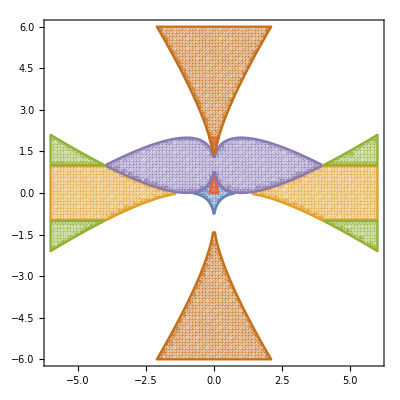

```mathematica
RegionPlot[{Subscript[KdFROC, 1][x,y],Subscript[KdFROC, 2][x,y],Subscript[KdFROC, 3][x,y],Subscript[KdFROC, 4][x,y],Subscript[KdFROC, 5][x,y],Subscript[KdFROC, 6][x,y]},{x,-6,6},{y,-6,6},PlotPoints->100]
```